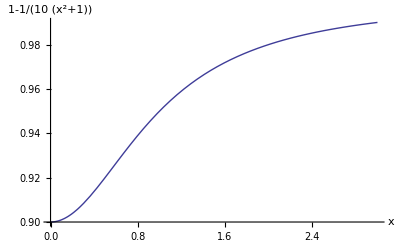

```mathematica
k[x_, a_] := 1 - a/(1 + x^2)

p = Module[ {a},
a  = 1/10 ;
Plot[
k[x, a], {x, 0, 3}
, PlotRange -> Full
, AxesLabel -> {x, 1-a/(x^2+1)}
]]
(*SetDirectory["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit"]
Export[ "modernOpticsLecture20Fig5.pdf", p]
*)
```